Phonon Modes for Lattice Vibrations with One-Atom Basis

A lattice of atoms can be modelled as harmonic oscillators, with forces proportional to the displacements of the atoms from equilibrium positions.  The simplest such model introduces coupling for only the nearest neighbor atoms.  In this demonstration, a lattice cell containing a single atom is modelled, with nearest neighbor harmonic coupling to the mass in each nearby cell.  Normal mode solutions to these equations of motion are plotted.  Controls are provided to alter the coupling "spring constants" and other free parameters, as well as controls to select from the reciprocal space vectors, and angular frequencies associated with the normal mode solutions.  A time control is also provided to display changes of the lattice through one period of the lattice vibration.

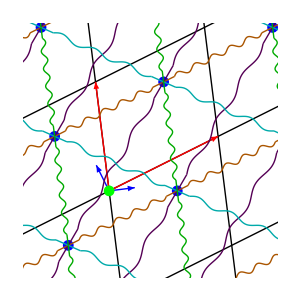

The positions of masses within a periodic array of cells, can be described by summing the lattice vector (r⃗)_(n⃗ = (n_1, n_2)) = n_1 a⃗ + n_2 b⃗, representing the origin of each of the lattice cell, and a relative vector to the position of each of the masses.  With (p⃗)_k representing the equilibrium position of k^th mass in cell (r⃗)_(n⃗), the position of that mass is (r⃗)_(n⃗)+ (p⃗)_k.

Let (a⃗)_(n⃗,k;m⃗',j)= (r⃗)_(n⃗)+(p⃗)_k - (r⃗)_(m⃗)-(p⃗)_j  represent the equilibrium separation of the k^th mass in cell (r⃗)_(n⃗) from the  j^th mass in cell (r⃗)_(m⃗), with the unit vector for that separation (â)_(n⃗,k;m⃗',j).  If the harmonic coupling between these masses has magnitude K_(n⃗,k;m⃗',j), then the system of equations describing the vector displacement (u⃗)_(n, k) for the k^th mass in unit cell n⃗ from the equilibrium position is given by

m_k OverVector[u^(..)]_(n⃗, k)= -∑_(n⃗,k ≠ m⃗',j) K_(n⃗,k;m⃗',j)Proj_((â)_(n⃗,k;m⃗',j)) ((u⃗)_(n⃗, k)- (u⃗)_(m⃗, j))^2

In general, we have one such equation for each n⃗, k pair.  However, a trial solution of the form: (u⃗)_(n⃗, k)(t)= ((ϵ⃗)_k(q⃗))/(√m_k) e^(I ((r⃗)_(n⃗). q⃗ - ω t)) can be used to decouple this system, so that n⃗ can be fixed at (0,0).  This results in a single equation for each k^th mass, the solutions of which are called normal mode solutions, describing all the steady state lattice vibrations that can be modelled by the trial solution above.  The rank of the resulting eigenvalue problem depends on the number of masses per unit cell, but the complexity of the matrix expression depends on the number of neighbouring interactions that are considered.  For example, given lattice vectors a⃗, b⃗, diagonals r⃗=a⃗ + b⃗, s⃗=a⃗ - b⃗ , and a one atom basis, where each unit cell contains a single mass coupled with harmonic oscillator forces between only nearest neighbours, the normal mode solutions follow from the solution of the eigenvalue problem

(ω^2 | 0
0 | ω^2) ϵ⃗ = 4/m( k_1 â (â)^T sin^2( a⃗ . q⃗/2 ) +  k_2 b̂ (b̂)^T sin^2( b⃗ . q⃗/2 ) +  k_3 r̂ (r̂)^T sin^2( ( b⃗ + a⃗ ). q⃗/2 ) +  k_4 ŝ (ŝ)^T sin^2( ( b⃗ - a⃗ ). q⃗/2 ))ϵ⃗

Here q⃗ is a vector in reciprocal space, effectively parameterizing the angular velocity ω = ω(q⃗).  The vector ϵ⃗(q) is an eigenvector of the equations of motion of the system for this assumed solution, where ω^2 are the eigenvalues of this system.  For such a one atom basis, there are two such ω^2 eigenvalues per q⃗ point, each with a different characteristic motion.

Controls are provided to display the dynamics associated with each of the characteristic angular frequencies ω, for given reciprocal vector values q⃗.

Three tabs are provided in this demonstration.  The primary tab provides plots the solution for particular q⃗ point, and one of the angular velocity eigenvalues for that  q⃗ point.  In that tab, selecting run for the time control will animate the lattice vibrations.  A second tab provides the dispersion relation, the dependence of angular velocity ω(q⃗) on all  q⃗ points.   Finally, a parameters tab provides controls for the spring constants K_(n⃗,k;m⃗',j), the primitive unit cell lattice vectors a⃗,b⃗, and the positions of the masses (p⃗)_k within each unit cell of the lattice.

General theory describing oscillations around the lattice equilibrium points can be found in:

Neil W Ashcroft and N David Mermin. Solid State Physics. Holt, Rinehart and Winston, New York, 1976.  Chapters 21, 22.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

one atom basis, lattice vibration, phonon, reciprocal lattice vector, angular frequency

Analysis of Lattice Vibrations in Two Dimensions

Motion of Atoms in Crystal

Simple Harmonic Motion for a Spring

Normal Modes in a Periodic Square Lattice

Contributed by: Peeter Joot